## Интерактивное исследование форматов данных

WolframAlpha["запрос", формат] - отправляет запрос в Wolfram|Alpha и возвращает результат в заданном формате
При использовании формата "Input" дает левую часть уравнения или вывод вычислений на языке Wolfram Language
При использовании формата "Output" дает правую часть уравнения или вывод вычислений на языке Wolfram Language
При использовании формата "FormatData" дает полное уравнение в стандартном синтаксисе языка Wolfram Language

ReleaseHold[expr] - удаляет один слой Hold,HoldForm,HoldPattern и HoldComplete (все стандартные неоцененные контейнеры) в выражении expr. % - дает последний полученный результат

HoldComplete[∫_(-2 π)^(2 π) Cos[x]ⅆx]

HoldComplete[0]

Hold[∫_(-2 π)^(2 π) Cos[x]ⅆx==0]

HoldComplete[Plot[Cos[x],{x,-2 π,2 π}]]

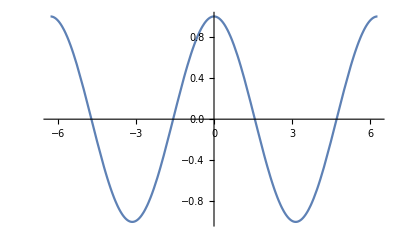

```mathematica
WolframAlpha["integrate cosx from -2pi to 2pi", {{"Input",1},"Input"}]
WolframAlpha["integrate cosx from -2pi to 2pi", {{"Input",1},"Output"}]
WolframAlpha["integrate cosx from -2pi to 2pi", {{"Input",1},"FormulaData"}]
WolframAlpha["integrate cosx from -2pi to 2pi", {{"VisualRepresentationOfTheIntegral", 1}, "Input"}]
ReleaseHold[%]
```

2. Открытые форматы данных не обязательно похожи на графический результат

Запрос ниже должен вычислять акции amazon за указанный период, в 1 столбце дата трасформированная Wolfram|Alpha, во втором цена 1 акции amazon, в третем - история стоимости акций за указ период на графике

```mathematica
WolframAlpha["amazon close Jan 5, 2020 to Jan 21 2020"]
```

WolframAlphaQueryResults

```mathematica
3. Структура второго аргумента
```

3. второго Структура аргумента

```mathematica
(*WolframAlpha[{"podid","subpodid"}, "property"]
podid - строка, созданная Wolfram|Alpha для идентификации модуля
subpodid - представляетсобой целое число,указывающее положение конкретного результата в модуле
property - напрямую запрашивает доступные форматы данных для podid*)
```

```mathematica
{WolframAlpha["plot tgx", {{"Plot", 1}, "Input"}], 
 WolframAlpha["plot tgx", {{"Plot", 2}, "Input"}]}
```

{HoldComplete[Plot[Tan[x],{x,-π,π}]],HoldComplete[Plot[Tan[x],{x,-4 π,4 π}]]}

```mathematica
4. Свободная форма ввода
```

4. ввода форма Свободная

```mathematica
(*Например, чтобы получить доступ к вычислимым данным для интеграла из Примера 1 в задании 1,достаточно щёлкнуть по нему правой кнопкой мыши и выбрать Copy As -> Input text*)
```

```mathematica
∫_1^π (Cos[x]+Sin[x])ⅆx
```

1+Cos[1]-Sin[1]

```mathematica
Получение форматов данных программными методами
```

данных методами форматов Получение программными

```mathematica
1. Форматы данных как свойства субмодуля
```

1. как данных Форматы свойства субмодуля

```mathematica
(*Имена программных свойств для различных форматов представляют собой строки,полученные из соответствующих имён меню путем объединения слов в одно целое: Computable data становится "ComputableData",Time series data становится "TimeSeriesData",Input становится "Input".*)
```

```mathematica
WolframAlpha["4+2*7-1",{{"Input",1},"FormulaData"}]
WolframAlpha["4+2*7",{{"Input",1},"ComputableData"}]
```

Hold[4+2 7-1]

Hold[4+2 7]

```mathematica
2. Определение доступных форматов
```

2. форматов доступных Определение

```mathematica
(*Форматы данных,доступные для конкретного субмодуля,содержатся в свойстве «DataFormats» каждого субмодуля.Это свойство можно вычислить так же,как и любое другое свойство вложенного модуля.*)
```

```mathematica
WolframAlpha["plot cosx",{All,"DataFormats"}]
```

{{{Input,1},DataFormats}→{Plaintext,Input},{{Plot,1},DataFormats}→{Input},{{Plot,2},DataFormats}→{Input}}

```mathematica
3. Прямые запросы данных
```

3. Прямые данных запросы

В WolframAlpha["podid","property"]
  podid - строка, созданная Wolfram|Alpha для идентификации модуля
   property - напрямую запрашивает доступные форматы данных для podid
   
   Если запросить определенные свойства всех модулей, появятся только те модули,которые действительно содержат эти форматы:

```mathematica
WolframAlpha["2+2","PodIDs"]
```

{Input,Result,NumberLine,NumberName,Illustration,TypicalHumanComputationTimes}

запрашиваем определенные форматы из определенного subpod.В этом случае (когда в спецификации нет All),если конкретный формат недоступен,вы получите правило для него с правой частью Missing["NotAvailable"]:

```mathematica
WolframAlpha["2+5",{{"Result",1},{"Output","FormulaData"}}]
```

{{{Result,1},Output}→HoldComplete[7],{{Result,1},FormulaData}→Hold[7]}

## Примеры открытых данных

```mathematica
1. Величины и числа
```

1. и числа Величины

```mathematica
(*  Показывает все данные об акциях и их измерениях в указанном промежутке в виде таблицы*)
WolframAlpha["amazon close Jan 5, 2020 to Jan 21 2020",{{"Result",1},"FormattedData"}]
(*  Показывает все данные об акциях и их измерениях в виде списка списков *)
WolframAlpha["amazon close Jan 5, 2020 to Jan 21 2020",{{"Result",1},"ComputableData"}]
(*  Показывает все данные об акциях в виде списка чисел *)
WolframAlpha["amazon close Jan 5, 2020 to Jan 21 2020",{{"Result",1},"NumberData"}]
(*  Показывает данные об акциях в виде списка  стоимостей *)
WolframAlpha["amazon close Jan 5, 2020 to Jan 21 2020",{{"Result",1},"QuantityData"}]
```

mean | 94.29 $
highest | 95.34 $
lowest | 93.10 $
volatility | 14. %
change | -0.57 %

{{mean,94.29 $},{highest,95.34 $},{lowest,93.10 $},{volatility,14. %},{change,-0.57 %}}

{94.29,95.34,93.1,14.,-0.57}

{94.29 $,95.34 $,93.10 $,14. %,-0.57 %}

```mathematica
3. Временные ряды
```

3. ряды Временные

```mathematica
(* Исторические графики являются прототипом временных рядов,которые дают значение для каждого элемента в списке дат.
```

```mathematica
WolframAlpha["amazon close Jan 5, 2020 to Jan 21 2020",IncludePods->"DateRangeSpecified:Close:FinancialData"]
```

WolframAlphaQueryResults

```mathematica
(* показывает данные в виде вычисляемых данных *)
WolframAlpha["amazon close Jan 5, 2020 to Jan 21 2020",{{"DateRangeSpecified:Close:FinancialData",1},"ComputableData"}]
```

{{{2020,1,6,0,0,0.},95.14 $},{{2020,1,7,0,0,0.},95.34 $},{{2020,1,8,0,0,0.},94.60 $},{{2020,1,9,0,0,0.},95.05 $},{{2020,1,10,0,0,0.},94.16 $},{{2020,1,13,0,0,0.},94.57 $},{{2020,1,14,0,0,0.},93.47 $},{{2020,1,15,0,0,0.},93.10 $},{{2020,1,16,0,0,0.},93.90 $},{{2020,1,17,0,0,0.},93.24 $},{{2020,1,21,0,0,0.},94.60 $}}

```mathematica
4. Формулы
```

4. Формулы

```mathematica
(*Поиск теоремы косинусов и вывод информации о ней*)
WolframAlpha["Law of cosines",{{"Equation",1},"FormattedData"}]
```

Hold[c^2==a^2+b^2-2 a b Cos[γ] | ] | 
Hold[c] | third side length
Hold[a] | first side length
Hold[b] | second side length
Hold[γ] | angle opposite third side

```mathematica
5. Звуки
```

5. Звуки

```mathematica
(* При помощи WolframAlpha выводим гамму ля мажор
```

```mathematica
WolframAlpha["a-major scale",IncludePods->"MusicNotation"]
```

WolframAlphaQueryResults

```mathematica
(* вывод гаммы ля мажор в аудио дорожку
```

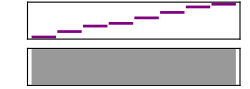

```mathematica
WolframAlpha["а-major scale",{{"MusicNotation",1},"SoundData"}]
```